```mathematica
PacletDirectoryAdd["~/github/EcoEvo"];
<<EcoEvo`
```

PacletDirectoryAdd::expobs: The experimental function PacletDirectoryAdd is now obsolete and is superseded by PacletDirectoryLoad.

EcoEvo Package Version 1.8.0 (June 16, 2023)
Christopher A. Klausmeier <christopher.klausmeier@gmail.com>

```mathematica
SetModel[{
Pop[n]->{Equation:>n(1-n/nk)-an p n/(n+h),Color->Green},
Pop[p]->{Equation:>p(apred n/(n+h)-mp),Color->Red},
Parameters:>{an>0,apred>0,h>0,mp>0,nk>0}
}];
```

```mathematica
RuleListSet@{an->1,apred->2,h->1,mp->1,nk->2}
Clear[nk]
```

```mathematica
EcoEqns[]
```

{n'==n (1-n/nk)-(n p)/(1+n),p'==(-1+(2 n)/(1+n)) p}

```mathematica
debug=False;
tr=TrackEq[EcoEqns[],{nk->1.1},{n->1,p->0.181818},{nk,1,4}]
```

{{n→InterpolatingFunction[…],p→InterpolatingFunction[…],Eigenvalues→InterpolatingFunction[…]},{n→InterpolatingFunction[…],p→InterpolatingFunction[…],Eigenvalues→InterpolatingFunction[…]}}

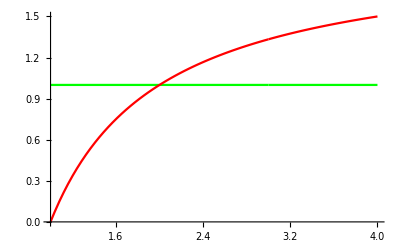

```mathematica
PlotRuleList[tr,{n,p}]
```

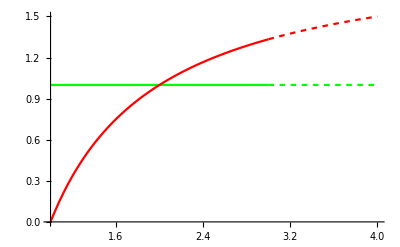

```mathematica
Show[
PlotRuleList[tr[[1]],{n,p}],
PlotRuleList[tr[[2]],{n,p},LineStyles->Dashing[0.01]],
PlotRange->All
]
```

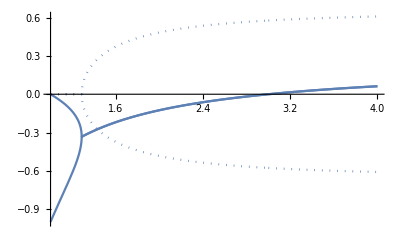

```mathematica
PlotRuleList[tr,Eigenvalues]
```

```mathematica
FinalSlice[tr[[1]]]
InitialSlice[tr[[2]]]
```

{n→1.,p→1.33333,Eigenvalues→{4.83706×10^-9+0.57735 ⅈ,4.83706×10^-9-0.57735 ⅈ}}

{n→1.,p→1.33333,Eigenvalues→{4.83706×10^-9+0.57735 ⅈ,4.83706×10^-9-0.57735 ⅈ}}

```mathematica
Slice[tr[[2]],3.2]
```

{n→1.,p→1.375,Eigenvalues→{0.0156248+0.586093 ⅈ,0.0156248-0.586093 ⅈ}}